```mathematica
guangzhouData22=WeatherData["Guangzhou","Temperature",{{2022,1,1},{2022,12,31},"Day"}]
guangzhouData21=WeatherData["Guangzhou","Temperature",{{2021,1,1},{2021,12,31},"Day"}]
```

TimeSeries[…]

TimeSeries[…]

```mathematica
guangzhouListData22=QuantityMagnitude[guangzhouData22["Values"]]~TakeList~(Values[Counts[DateList[#][[2]]&/@guangzhouData22["Dates"]]]);
guangzhouListData21=QuantityMagnitude[guangzhouData21["Values"]]~TakeList~(Values[Counts[DateList[#][[2]]&/@guangzhouData21["Dates"]]]);
```

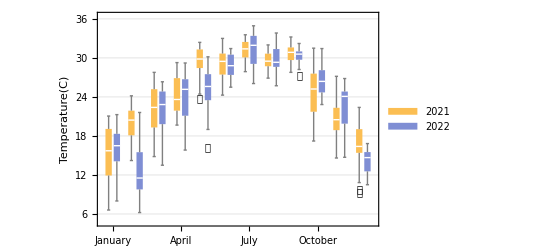

```mathematica
BoxWhiskerChart[{guangzhouListData21,guangzhouListData22}//Transpose,{{"Outliers","〇"}},
ChartLegends->{"2021","2022"},
PlotTheme->"Detailed",
BarSpacing->{Small,Large},ChartLabels->{Rotate[#,π/2]&/@
{"January","February","March","April","May","June","July","August","September","October","November","December"},{None,None}},
FrameLabel->{None,"Temperature(C)"}]
```

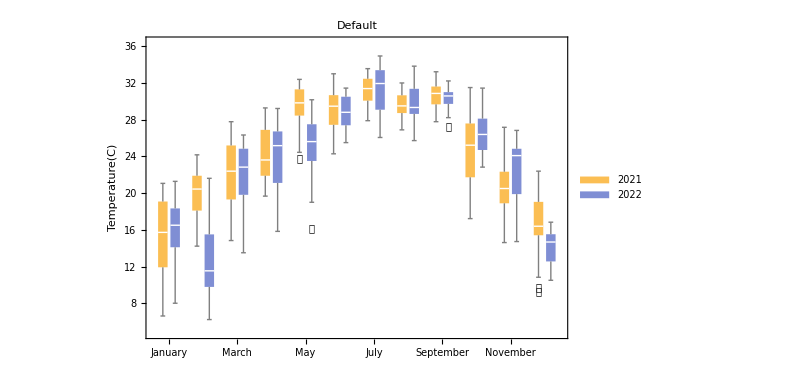
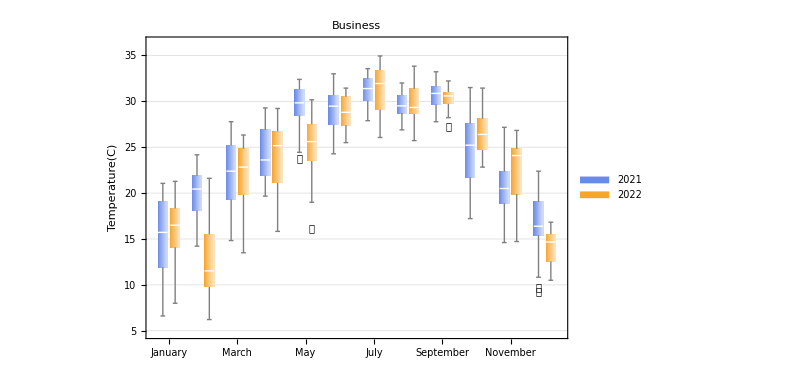
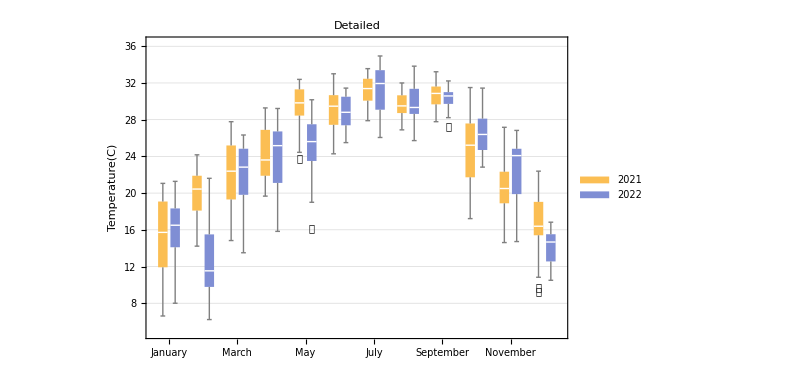
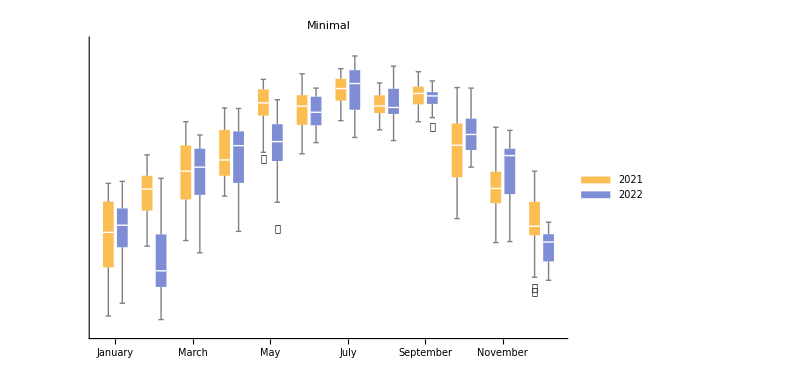
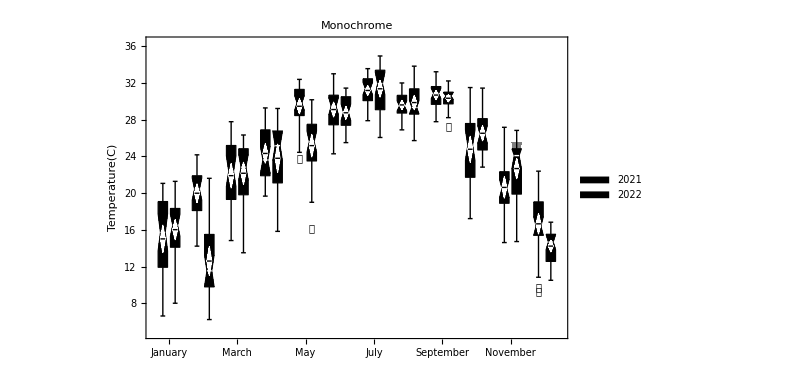
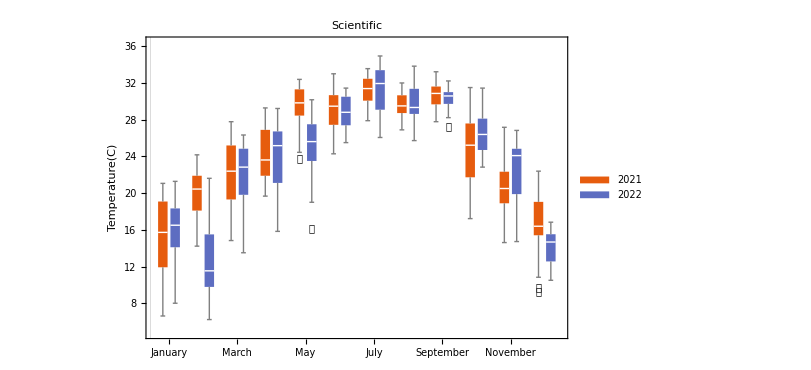
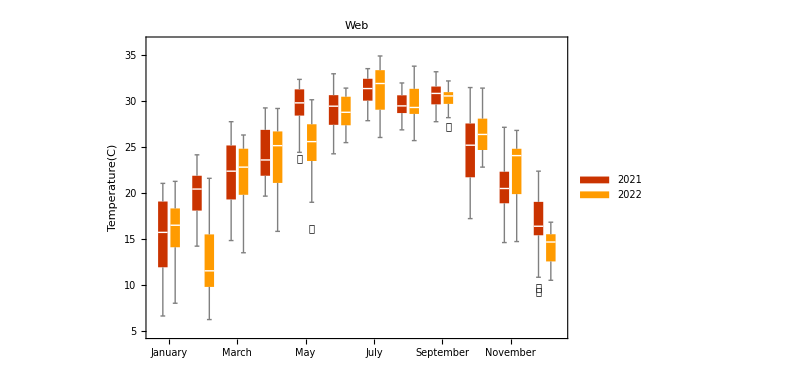
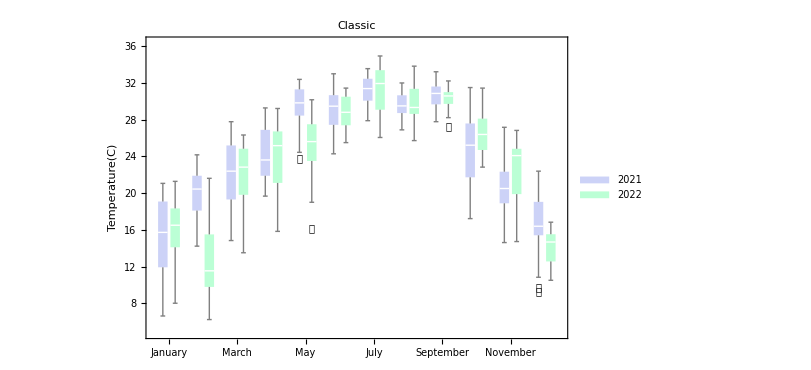
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
imgList=BoxWhiskerChart[{guangzhouListData21,guangzhouListData22}//Transpose,{{"Outliers","〇"}},ChartLegends->{"2021","2022"},BarSpacing->{Small,Large},ChartLabels->{Rotate[#,π/2,{Right,Top}]&/@{"January","February","March","April","May","June","July","August","September","October","November","December"},{None,None}},FrameLabel->{None,"Temperature(C)"},PlotTheme->#,PlotLabel->Text[#],ImageSize->600]&/@{"Default","Business","Marketing","Detailed","Minimal","Monochrome","Scientific","Web","Classic"}
```

```mathematica
Export[("E:\\Blog-DEMO\\blog-demo\\source\\media\\mathematica\\"<>ToString[#]<>".png"),imgList[[#-3]],"PNG"]&/@Range[4,Length[imgList]+3]
```

{E:\Blog-DEMO\blog-demo\source\media\mathematica\4.png,E:\Blog-DEMO\blog-demo\source\media\mathematica\5.png,E:\Blog-DEMO\blog-demo\source\media\mathematica\6.png,E:\Blog-DEMO\blog-demo\source\media\mathematica\7.png,E:\Blog-DEMO\blog-demo\source\media\mathematica\8.png,E:\Blog-DEMO\blog-demo\source\media\mathematica\9.png,E:\Blog-DEMO\blog-demo\source\media\mathematica\10.png,E:\Blog-DEMO\blog-demo\source\media\mathematica\11.png,E:\Blog-DEMO\blog-demo\source\media\mathematica\12.png}